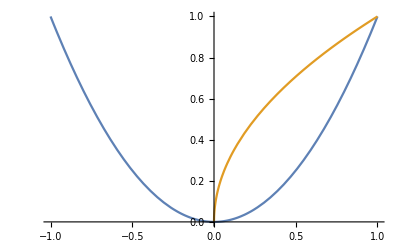

```mathematica
Plot[{x^2,x^(1/2)},{x,-1,1}]
```

```mathematica
D[x^1.1,x]
```

1.1 x^0.1

```mathematica
Plot3D[{Max[x,y],Log[ⅇ^x+ⅇ^y]},{x,0,10},{y,0,10}]
```

-Graphics3D-

```mathematica
Plot3D[Max[x,y]-Log[ⅇ^x+ⅇ^y],{x,0,10},{y,0,10}]
```

-Graphics3D-

```mathematica
Plot3D[( -Log[ⅇ^(-x)+ⅇ^(-y)]) -  (Min[x,y] - Log[1 + ⅇ^(Min[x,y]-Max[x,y])]),{x,0,10},{y,0,10}]
```

-Graphics3D-

```mathematica
Plot3D[{(Min[x,y] - Log[1 + ⅇ^(Min[x,y]-Max[x,y])]), -Log[ⅇ^(-x)+ⅇ^(-y)]},{x,0,10},{y,0,10}]
```

-Graphics3D-

```mathematica
Plot3D[( Log[ⅇ^(x)+ⅇ^(y)]) -  (Max[x,y] + Log[1 + ⅇ^(Min[x,y]-Max[x,y])]),{x,0,10},{y,0,10}]
```

-Graphics3D-

```mathematica
D[(vs*(m/((efq+fq)*fc*Log[ⅇ^(m/(fq*fc))+ⅇ^(em/(efq*efc))]))+vl*(m/((efq+fq)*fc*Log[ⅇ^(m/(fq*fc))+ⅇ^(em/(efq*efc))])))*Log[ⅇ^(m/(fq*fc))+ⅇ^(em/(efq*efc))],{{m,fq}}]
```

{(ⅇ^(m/(fc fq)) ((m vl)/(fc (efq+fq) Log[ⅇ^(em/(efc efq))+ⅇ^(m/(fc fq))])+(m vs)/(fc (efq+fq) Log[ⅇ^(em/(efc efq))+ⅇ^(m/(fc fq))])))/((ⅇ^(em/(efc efq))+ⅇ^(m/(fc fq))) fc fq)+(-(ⅇ^(m/(fc fq)) m vl)/((ⅇ^(em/(efc efq))+ⅇ^(m/(fc fq))) fc^2 fq (efq+fq) Log[ⅇ^(em/(efc efq))+ⅇ^(m/(fc fq))]^2)-(ⅇ^(m/(fc fq)) m vs)/((ⅇ^(em/(efc efq))+ⅇ^(m/(fc fq))) fc^2 fq (efq+fq) Log[ⅇ^(em/(efc efq))+ⅇ^(m/(fc fq))]^2)+vl/(fc (efq+fq) Log[ⅇ^(em/(efc efq))+ⅇ^(m/(fc fq))])+vs/(fc (efq+fq) Log[ⅇ^(em/(efc efq))+ⅇ^(m/(fc fq))])) Log[ⅇ^(em/(efc efq))+ⅇ^(m/(fc fq))],-(ⅇ^(m/(fc fq)) m ((m vl)/(fc (efq+fq) Log[ⅇ^(em/(efc efq))+ⅇ^(m/(fc fq))])+(m vs)/(fc (efq+fq) Log[ⅇ^(em/(efc efq))+ⅇ^(m/(fc fq))])))/((ⅇ^(em/(efc efq))+ⅇ^(m/(fc fq))) fc fq^2)+((ⅇ^(m/(fc fq)) m^2 vl)/((ⅇ^(em/(efc efq))+ⅇ^(m/(fc fq))) fc^2 fq^2 (efq+fq) Log[ⅇ^(em/(efc efq))+ⅇ^(m/(fc fq))]^2)+(ⅇ^(m/(fc fq)) m^2 vs)/((ⅇ^(em/(efc efq))+ⅇ^(m/(fc fq))) fc^2 fq^2 (efq+fq) Log[ⅇ^(em/(efc efq))+ⅇ^(m/(fc fq))]^2)-(m vl)/(fc (efq+fq)^2 Log[ⅇ^(em/(efc efq))+ⅇ^(m/(fc fq))])-(m vs)/(fc (efq+fq)^2 Log[ⅇ^(em/(efc efq))+ⅇ^(m/(fc fq))])) Log[ⅇ^(em/(efc efq))+ⅇ^(m/(fc fq))]}

```mathematica
Simplify[(ⅇ^(m/(fc fq)) ((m vl)/(fc (efq+fq) Log[ⅇ^(em/(efc efq))+ⅇ^(m/(fc fq))])+(m vs)/(fc (efq+fq) Log[ⅇ^(em/(efc efq))+ⅇ^(m/(fc fq))])))/((ⅇ^(em/(efc efq))+ⅇ^(m/(fc fq))) fc fq)+(-(ⅇ^(m/(fc fq)) m vl)/((ⅇ^(em/(efc efq))+ⅇ^(m/(fc fq))) fc^2 fq (efq+fq) Log[ⅇ^(em/(efc efq))+ⅇ^(m/(fc fq))]^2)-(ⅇ^(m/(fc fq)) m vs)/((ⅇ^(em/(efc efq))+ⅇ^(m/(fc fq))) fc^2 fq (efq+fq) Log[ⅇ^(em/(efc efq))+ⅇ^(m/(fc fq))]^2)+vl/(fc (efq+fq) Log[ⅇ^(em/(efc efq))+ⅇ^(m/(fc fq))])+vs/(fc (efq+fq) Log[ⅇ^(em/(efc efq))+ⅇ^(m/(fc fq))])) Log[ⅇ^(em/(efc efq))+ⅇ^(m/(fc fq))]]
```

(vl+vs)/(efq fc+fc fq)

```mathematica
Simplify[-(ⅇ^(m/(fc fq)) m ((m vl)/(fc (efq+fq) Log[ⅇ^(em/(efc efq))+ⅇ^(m/(fc fq))])+(m vs)/(fc (efq+fq) Log[ⅇ^(em/(efc efq))+ⅇ^(m/(fc fq))])))/((ⅇ^(em/(efc efq))+ⅇ^(m/(fc fq))) fc fq^2)+((ⅇ^(m/(fc fq)) m^2 vl)/((ⅇ^(em/(efc efq))+ⅇ^(m/(fc fq))) fc^2 fq^2 (efq+fq) Log[ⅇ^(em/(efc efq))+ⅇ^(m/(fc fq))]^2)+(ⅇ^(m/(fc fq)) m^2 vs)/((ⅇ^(em/(efc efq))+ⅇ^(m/(fc fq))) fc^2 fq^2 (efq+fq) Log[ⅇ^(em/(efc efq))+ⅇ^(m/(fc fq))]^2)-(m vl)/(fc (efq+fq)^2 Log[ⅇ^(em/(efc efq))+ⅇ^(m/(fc fq))])-(m vs)/(fc (efq+fq)^2 Log[ⅇ^(em/(efc efq))+ⅇ^(m/(fc fq))])) Log[ⅇ^(em/(efc efq))+ⅇ^(m/(fc fq))]]
```

-(m (vl+vs))/(fc (efq+fq)^2)

```mathematica
Simplify[(vs*(m/((efq+fq)*fc*Log[ⅇ^(m/(fq*fc))+ⅇ^(em/(efq*efc))]))+vl*(m/((efq+fq)*fc*Log[ⅇ^(m/(fq*fc))+ⅇ^(em/(efq*efc))])))*Log[ⅇ^(m/(fq*fc))+ⅇ^(em/(efq*efc))]]
```

(m (vl+vs))/(fc (efq+fq))

```mathematica
Block[{rnd = Log[ⅇ^(k*m/(fq*fc))+ⅇ^(k*em/(efq*efc))]/k},
Simplify[(vs*(m/(m+efq*fc*rnd))+vl*(1-m/(m+efq*fc*rnd)))]]
```

(k m vs+efq fc vl Log[ⅇ^((em k)/(efc efq))+ⅇ^((k m)/(fc fq))])/(k m+efq fc Log[ⅇ^((em k)/(efc efq))+ⅇ^((k m)/(fc fq))])

```mathematica
FullSimplify[D[(Log[ⅇ^((em k)/(efc efq))+ⅇ^((k m)/(fc fq))] (k m vs+efq fc vl Log[ⅇ^((em k)/(efc efq))+ⅇ^((k m)/(fc fq))]))/(k (k m+efq fc Log[ⅇ^((em k)/(efc efq))+ⅇ^((k m)/(fc fq))])),{{m,fq}}]]
```

{(ⅇ^((k m)/(fc fq)) k^2 m^2 vs+efq fc Log[ⅇ^((em k)/(efc efq))+ⅇ^((k m)/(fc fq))] (2 ⅇ^((k m)/(fc fq)) k m vl+fc (-ⅇ^((em k)/(efc efq)) fq (vl-vs)+ⅇ^((k m)/(fc fq)) (efq vl-fq vl+fq vs)) Log[ⅇ^((em k)/(efc efq))+ⅇ^((k m)/(fc fq))]))/((ⅇ^((em k)/(efc efq))+ⅇ^((k m)/(fc fq))) fc fq (k m+efq fc Log[ⅇ^((em k)/(efc efq))+ⅇ^((k m)/(fc fq))])^2),-(ⅇ^((k m)/(fc fq)) m (k^2 m^2 vs+efq fc vl Log[ⅇ^((em k)/(efc efq))+ⅇ^((k m)/(fc fq))] (2 k m+efq fc Log[ⅇ^((em k)/(efc efq))+ⅇ^((k m)/(fc fq))])))/((ⅇ^((em k)/(efc efq))+ⅇ^((k m)/(fc fq))) fc fq^2 (k m+efq fc Log[ⅇ^((em k)/(efc efq))+ⅇ^((k m)/(fc fq))])^2)}

```mathematica
FullSimplify[ⅇ^((k m)/(fc fq))/(ⅇ^((em k)/(efc efq))+ⅇ^((k m)/(fc fq)))]
```

1/(1+ⅇ^((em k)/(efc efq)-(k m)/(fc fq)))

```mathematica
FullSimplify[(ⅇ^((k m)/(fc fq)) k^2 m^2 vs+efq fc Log[ⅇ^((em k)/(efc efq))+ⅇ^((k m)/(fc fq))] (2 ⅇ^((k m)/(fc fq)) k m vl+fc (-ⅇ^((em k)/(efc efq)) fq (vl-vs)+ⅇ^((k m)/(fc fq)) (efq vl-fq vl+fq vs)) Log[ⅇ^((em k)/(efc efq))+ⅇ^((k m)/(fc fq))]))/((ⅇ^((em k)/(efc efq))+ⅇ^((k m)/(fc fq))) fc fq (k m+efq fc Log[ⅇ^((em k)/(efc efq))+ⅇ^((k m)/(fc fq))])^2)]
```

(ⅇ^((k m)/(fc fq)) k^2 m^2 vs+efq fc Log[ⅇ^((em k)/(efc efq))+ⅇ^((k m)/(fc fq))] (2 ⅇ^((k m)/(fc fq)) k m vl+fc (-ⅇ^((em k)/(efc efq)) fq (vl-vs)+ⅇ^((k m)/(fc fq)) (efq vl-fq vl+fq vs)) Log[ⅇ^((em k)/(efc efq))+ⅇ^((k m)/(fc fq))]))/((ⅇ^((em k)/(efc efq))+ⅇ^((k m)/(fc fq))) fc fq (k m+efq fc Log[ⅇ^((em k)/(efc efq))+ⅇ^((k m)/(fc fq))])^2)

```mathematica
Plot3D[{Min[x,y],-Log[ⅇ^-x+ⅇ^-y]},{x,0,10},{y,0,10}]
```

-Graphics3D-

```mathematica
Block[{mv = -Log[ⅇ^(-fq*k)+ⅇ^(-m*k/fc)]/k},FullSimplify[vs*mv/(mv+efq) + vl*efq/(mv+efq)]]
```

vs+(efq k (-vl+vs))/(-efq k+Log[ⅇ^(-fq k)+ⅇ^(-(k m)/fc)])

```mathematica
Block[{mv = -Log[ⅇ^(-fq*k)+ⅇ^(-m*k/fc)]/k},FullSimplify[D[vs*mv/(mv+efq) + vl*efq/(mv+efq),{{m,fq}}]]]
```

{-(ⅇ^(fq k) efq k^2 (vl-vs))/((ⅇ^(fq k)+ⅇ^((k m)/fc)) fc (-efq k+Log[ⅇ^(-fq k)+ⅇ^(-(k m)/fc)])^2),-(ⅇ^((k m)/fc) efq k^2 (vl-vs))/((ⅇ^(fq k)+ⅇ^((k m)/fc)) (-efq k+Log[ⅇ^(-fq k)+ⅇ^(-(k m)/fc)])^2)}

```mathematica
Block[{m=fq*fc},FullSimplify[D[vs*fq/(fq+efq) + vl*efq/(fq+efq),fq]]]
```

(efq (-vl+vs))/(efq+fq)^2

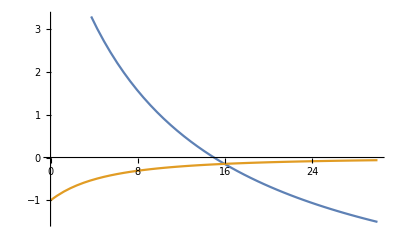

```mathematica
Block[{k = 4, fc = 0.1, efq =10, vs = -4, vl = 6, m=fq*fc,},Plot[{vs*fq/(fq+efq) + vl*efq/(fq+efq),(efq (-vl+vs))/(efq+fq)^2},{fq,0,30}]]
```

```mathematica
Block[{k = 4, fc = 2, efq =15, vs = -10, vl = 5,mv = -Log[ⅇ^(-fq*k)+ⅇ^(-m*k/fc)]/k},Plot3D[vs*mv/(mv+efq) + vl*efq/(mv+efq),{m,0,30},{fq,0,30}]]
```

-Graphics3D-

```mathematica
Block[{u=(nt-np-nn-nl)*np/(nn+np),ss=(nt-np-nn-nl)*np/(nn+np)*(1-np/(nn+np))},Integrate[ⅇ^-((x-u)^2/(2*ss))/(2*ss*π)^(1/2),x]]
```

(√nn √np √(nl+nn+np-nt) Erfi[(nl np+nn (np+x)+np (np-nt+x))/(√2 √nn √np √(nl+nn+np-nt))])/(2 (nn+np) √(-(nn np (nl+nn+np-nt))/(nn+np)^2))

```mathematica
pdintegral[x_, nt_,np_,nn_,nl_]:=Erf[(x-(nt-np-nn-nl)*np/(nn+np))/(2*(nt-np-nn-nl)*(np/(nn+np))*(1-np/(nn+np)))^(1/2)]/2
```

```mathematica
Definition[pdintegral]
```

pdintegral[x_,nt_,np_,nn_,nl_]:=1/2 Erf[(x-((nt-np-nn-nl) np)/(nn+np))/(√((2 (nt-np-nn-nl) np (1-np/(nn+np)))/(nn+np)))]

```mathematica
Simplify[(pdintegral[nt-np-nn-nl,nt,np,nn,nl]-pdintegral[nt/2-np-a,nt,np,nn,nl])/(pdintegral[nt-np-nn-nl,nt,np,nn,nl]-pdintegral[0,nt,np,nn,nl])]
```

(Erf[((nn+np) √(-(nn np (nl+nn+np-nt))/(nn+np)^2))/(√2 np)]-Erf[(2 nl np-2 a (nn+np)+nn nt-np nt)/(2 √2 (nn+np) √(-(nn np (nl+nn+np-nt))/(nn+np)^2))])/(Erf[((nn+np) √(-(nn np (nl+nn+np-nt))/(nn+np)^2))/(√2 nn)]+Erf[((nn+np) √(-(nn np (nl+nn+np-nt))/(nn+np)^2))/(√2 np)])

```mathematica
Block[{pwin = (Erf[((nn+np) √(-(nn np (nl+nn+np-nt))/(nn+np)^2))/(√2 np)]-Erf[(2 nl np-2 a (nn+np)+nn nt-np nt)/(2 √2 (nn+np) √(-(nn np (nl+nn+np-nt))/(nn+np)^2))])/(Erf[((nn+np) √(-(nn np (nl+nn+np-nt))/(nn+np)^2))/(√2 nn)]+Erf[((nn+np) √(-(nn np (nl+nn+np-nt))/(nn+np)^2))/(√2 np)])},FullSimplify[vs*pwin+vl*(1-pwin)]]
```

(vl Erf[((nn+np) √(-(nn np (nl+nn+np-nt))/(nn+np)^2))/(√2 nn)]+vs Erf[((nn+np) √(-(nn np (nl+nn+np-nt))/(nn+np)^2))/(√2 np)]+(vl-vs) Erf[(2 nl np-2 a (nn+np)+nn nt-np nt)/(2 √2 (nn+np) √(-(nn np (nl+nn+np-nt))/(nn+np)^2))])/(Erf[((nn+np) √(-(nn np (nl+nn+np-nt))/(nn+np)^2))/(√2 nn)]+Erf[((nn+np) √(-(nn np (nl+nn+np-nt))/(nn+np)^2))/(√2 np)])

```mathematica
Block[{pwin =(Erf[((nn+np) √(-(nn np (nl+nn+np-nt))/(nn+np)^2))/(√2 np)]-Erf[(2 nl np-2 a (nn+np)+nn nt-np nt)/(2 √2 (nn+np) √(-(nn np (nl+nn+np-nt))/(nn+np)^2))])/(Erf[((nn+np) √(-(nn np (nl+nn+np-nt))/(nn+np)^2))/(√2 nn)]+Erf[((nn+np) √(-(nn np (nl+nn+np-nt))/(nn+np)^2))/(√2 np)])},FullSimplify[D[vs*pwin+vl*(1-pwin),a]]]
```

(ⅇ^((2 nl np-2 a (nn+np)+(nn-np) nt)^2/(8 nn np (nl+nn+np-nt))) √(2/π) (-vl+vs))/(√(-(nn np (nl+nn+np-nt))/(nn+np)^2) (Erf[((nn+np) √(-(nn np (nl+nn+np-nt))/(nn+np)^2))/(√2 nn)]+Erf[((nn+np) √(-(nn np (nl+nn+np-nt))/(nn+np)^2))/(√2 np)]))

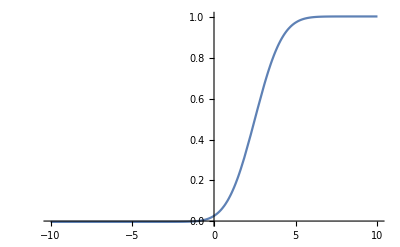

```mathematica
Block[{nn = 1, np = 1, nt= 14, nl=5,vs=10,vl=-5},Plot[(pdintegral[nt-np-nn-nl,nt,np,nn,nl]-pdintegral[nt/2-np-a,nt,np,nn,nl])/(pdintegral[nt-np-nn-nl,nt,np,nn,nl]-pdintegral[0,nt,np,nn,nl]),{a,-10,10}]]
```

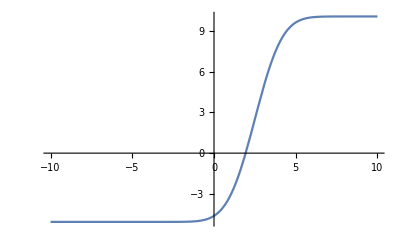

```mathematica
Block[{nn = 1, np = 1, nt= 14, nl=5,vs=10,vl=-5},Plot[(vl Erf[((nn+np) √(-(nn np (nl+nn+np-nt))/(nn+np)^2))/(√2 nn)]+vs Erf[((nn+np) √(-(nn np (nl+nn+np-nt))/(nn+np)^2))/(√2 np)]+(vl-vs) Erf[(2 nl np-2 a (nn+np)+nn nt-np nt)/(2 √2 (nn+np) √(-(nn np (nl+nn+np-nt))/(nn+np)^2))])/(Erf[((nn+np) √(-(nn np (nl+nn+np-nt))/(nn+np)^2))/(√2 nn)]+Erf[((nn+np) √(-(nn np (nl+nn+np-nt))/(nn+np)^2))/(√2 np)]),{a,-10,10}]]
```

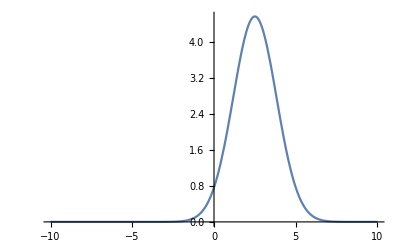

```mathematica
Block[{nn = 1, np = 1, nt= 14, nl=5,vs=10,vl=-5},Plot[(ⅇ^((2 nl np-2 a (nn+np)+(nn-np) nt)^2/(8 nn np (nl+nn+np-nt))) √(2/π) (-vl+vs))/(√(-(nn np (nl+nn+np-nt))/(nn+np)^2) (Erf[((nn+np) √(-(nn np (nl+nn+np-nt))/(nn+np)^2))/(√2 nn)]+Erf[((nn+np) √(-(nn np (nl+nn+np-nt))/(nn+np)^2))/(√2 np)])),{a,-10,10}]]
```

```mathematica
N[ⅇ^160]
```

3.06985×10^69

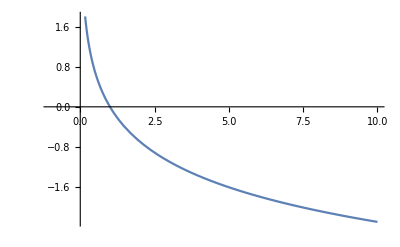

```mathematica
Plot[-Log[x],{x,-1,10}]
```

```mathematica
D[-Log2[x],x]
```

-1/(x Log[2])

```mathematica
N[Log[2]]
```

0.693147

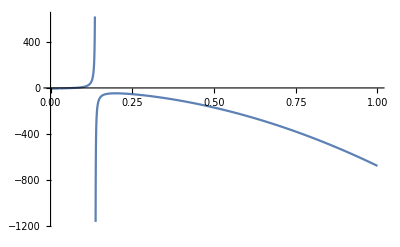

```mathematica
Block[{v1 =9.999624,v2=0.74840437,v3=-0.101654059,v4=2.11245768,v5=0.5335461,v6=0.023380764,v7=0,v8=0.139137713, d1=3.76559657,d2=-26.62247867,d3=238.5290722,d4=25.3122211,d5=-11.1887368,d6=12.6641204,d7=0,d8=1.13102575, vvs = 5, vvf=-1, numtotal =9, numneg = 1, numpos = 2, numplayer = 3, rem=numtotal - numneg - numpos - numplayer, inner2=numneg*numpos*rem, inner1=inner2^(1/2),rt2=1.4142135623730950488016887242097, rt2pi=0.79788456080286535587989211986876,erf1=Erf[inner1/(numneg*rt2)], erf2=Erf[inner1/(numpos*rt2)],denom=erf1+erf2, av4 = v4+x*d4, num=2.0*numplayer*numpos-2.0*av4*(numneg+numpos)+numneg*numtotal-numpos*numtotal, av5 = v5+x*d5, mvs = 4, mvf = -6,  fc = 0.1, efq = 10, fq = av5 / fc, tfq = efq+fq},
Plot[-0.1*(v1+x*d1)+
-0.2*(v2+x*d2)+
-vvs*erf1+-vvf*erf2+(vvs-vvf)*Erf[num/(2.0*rt2*inner1)]/denom+
(-mvs*fq+-mvf*efq)/tfq +
If[v1+x*d1<0,-((v1+x*d1)^2),0]+If[v2+x*d2<0,-((v2+x*d2)^2),0]+If[v3+x*d3<0,-((v3+x*d3)^2),0],{x,0,1}]]
```

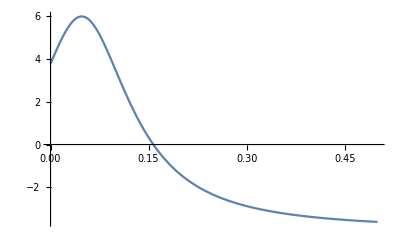

```mathematica
Block[{v1 =9.999624,v2=0.74840437,v3=-0.101654059,v4=2.11245768,v5=0.5335461,v6=0.023380764,v7=0,v8=0.139137713, d1=3.76559657,d2=-26.62247867,d3=238.5290722,d4=25.3122211,d5=-11.1887368,d6=12.6641204,d7=0,d8=1.13102575, vvs = 5, vvf=-1, numtotal =9, numneg = 1, numpos = 2, numplayer = 3, rem=numtotal - numneg - numpos - numplayer, inner2=numneg*numpos*rem, inner1=inner2^(1/2),rt2=1.4142135623730950488016887242097, rt2pi=0.79788456080286535587989211986876,erf1=Erf[inner1/(numneg*rt2)], erf2=Erf[inner1/(numpos*rt2)],denom=erf1+erf2, av4 = v4+x*d4, num=2.0*numplayer*numpos-2.0*av4*(numneg+numpos)+numneg*numtotal-numpos*numtotal, av5 = v5+x*d5, mvs = 4, mvf = -6,  fc = 0.1, efq = 10, fq = av5 / fc, tfq = efq^2+fq^2},
Plot[(-mvs*fq^2+-mvf*efq^2)/tfq ,{x,0,0.5}]]
```

```mathematica
Block[{fq = x/fc, tfq = efc^2+fq^2},D[(-vs*fq^2 + -vf*efq^2)/tfq,x]]
```

-(2 vs x)/(fc^2 (efc^2+x^2/fc^2))-(2 x (-efq^2 vf-(vs x^2)/fc^2))/(fc^2 (efc^2+x^2/fc^2)^2)